```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

```mathematica
<<BISfit`;
<<Data`;
<<Matcher`;
<<Classifier`;
Needs["PlotLegends`"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

```mathematica
(* check new nxr data,*)
```

```mathematica
data=nxrData[];
(*fd=Filterd[data[[9]]];*)
(*fdata=Map[Filterd,data];*)
(*fdata[[All,All,1]];*)
```

```mathematica
Dimensions[data]
```

{50,2,138,2}

```mathematica
(* now  normalize the data first*)
```

```mathematica
ffdata=Flatten[data,{{1,2},{3,4}}];
Dimensions[ffdata];
f1=Mean[ffdata];
f2=StandardDeviation[ffdata];
sdata=Standardize[ffdata];
nsdata=Reap[For[i=1;td=sdata,i≤Length[data],i++,
Sow[Take[td,2]];
td=Drop[td,2];
]][[2,1]];
Dimensions[nsdata]
fdata=nsdata;
```

{50,2,276}

```mathematica
(*Flatten[data,{{1},{2},{3,4}}];
Partition[%,{1,1,46}];
Flatten[%[[1,1,1]]];
pr=Partition[%,2];
Dimensions[%]
ListPlot[pr]*)
```

```mathematica
(*hs=Histogram[dsame,{0,20,0.2},"Probability",ColorFunction->Function[{x},Black]];
hd=Histogram[ddiff,{0,40,0.2},"Probability",ChartStyle->Opacity[0.5]*)(*,ColorFunction->Function[{x},Black]];*)
(*Histogram[{dsame,ddiff},{0,40,0.2},"Probability",ChartLayout->"Overlapped"];*)
```

```mathematica
(*initial functions*)
(*eucDist[pm_]:=Module[
{dsame,ddiff,i,j,k},
ddiff=Flatten[Reap[For[i=1,i≤Length[pm]-1,i++,
For[j=i+1,j≤Length[pm],j++,
Sow[Flatten[Outer[EuclideanDistance,pm[[i]],pm[[j]],1]]]
]]
][[2,1]]];
dsame=Reap[For[i=1,i≤Length[pm],i++,
For[j=1,j≤Length[pm[[i]]]-1,j++,
For[k=j+1,k<=Length[pm[[i]]],k++,
Sow[EuclideanDistance[pm[[i]][[j]],pm[[i]][[k]]]];
(*Sow[-Mdistance[fdata[[i]][[j]],fdata[[i]][[k]]]];*)
]]]
][[2,1]];
{ddiff,dsame}
];
*)
```

```mathematica
(* split 6 methods data*)
pdata=
Partition[fdata,{1,1,46}];
Dimensions[pdata];

pd=Flatten[pdata,{{1},{2},{3},{4,5,6}}];
Dimensions[%]
```

{50,2,6,46}

```mathematica
(* try first method :食指-中指*)
pm1=pd[[All,All,1]];
Dimensions[%]
```

{50,2,46}

```mathematica
pm=pm1;
Dimensions[%]
```

{50,2,46}

```mathematica
(* Euclidean distance distribution*)
```

```mathematica
{ddiff,dsame}=eucDist[pm];
{ns,nd}={Length[dsame],Length[ddiff]}
```

{50,4900}

```mathematica
Min[dsame]
Max[dsame]
mdsame=Mean[dsame]
ddsame=StandardDeviation[dsame]

Min[ddiff]
Max[ddiff]
mddiff=Mean[ddiff]
dddiff=StandardDeviation[ddiff]
```

0.25408

19.1646

1.98382

3.67036

0.151195

36.9521

7.54547

5.98641

```mathematica
dx=0.3;
dds=BinCounts[dsame,{0,20,dx}]/ns;
ddd=BinCounts[ddiff,{0,20,dx}]/nd;

dist=Table[i*dx,{i,0,Length[ddd]-1}];
pdds=Transpose[{dist,dds}];
pddd=Transpose[{dist,ddd}];
```

```mathematica
p50=ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.4}}];
```

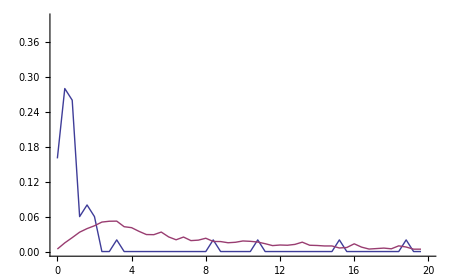
```mathematica
p50=-Graphics-;
```

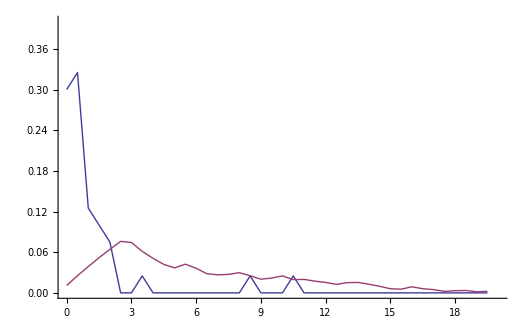
```mathematica
p40=-Graphics-;
```

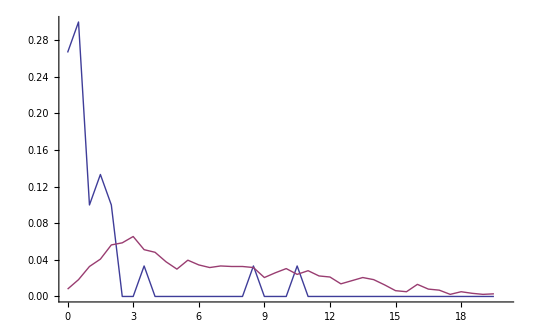
```mathematica
p30=-Graphics-;
```

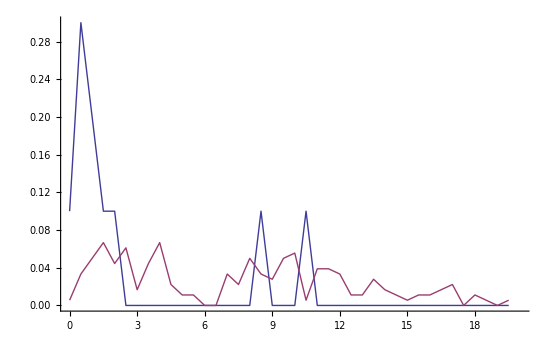
```mathematica
p10=-Graphics-;
```

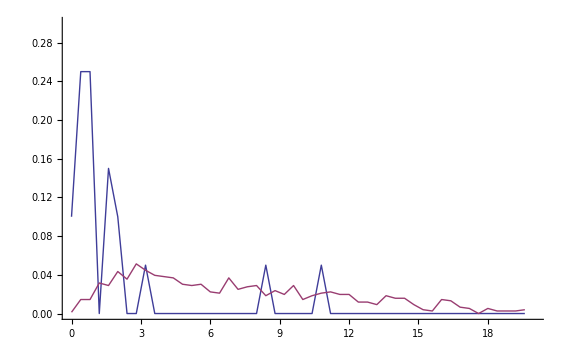
```mathematica
p20=-Graphics-;
```

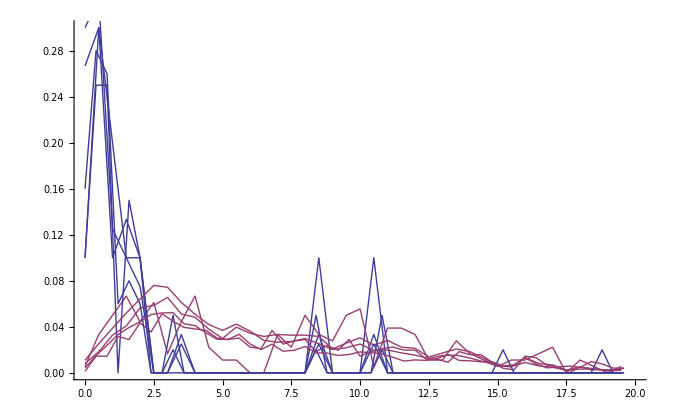

```mathematica
Show[p10,p20,p30,p40,p50]
```

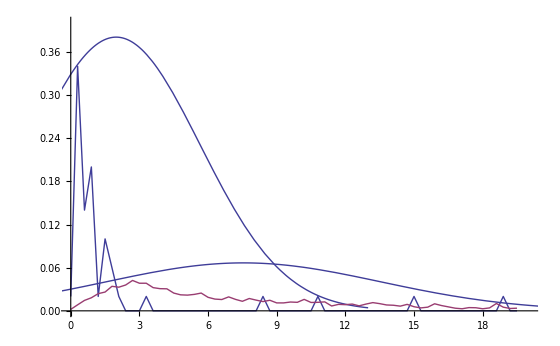

```mathematica
Ppdf1=Plot[3.5*PDF[NormalDistribution[mdsame,ddsame],x],{x,mdsame-3ddsame,mdsame+3ddsame}];

Ppdf2=Plot[1*PDF[NormalDistribution[mddiff,dddiff],x],{x,mddiff-3dddiff,mddiff+3dddiff}];

Show[Ppdf1,Ppdf2,p50,PlotRange->{{0,20},{0,0.4}}]
```

```mathematica
ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.3}},Frame->True,FrameLabel->{"Euclidean Distance","Percentage (%)"},PlotStyle->{{Dashed,Thickness[0.002]},{Dotted,Thickness[0.003]}},PlotLegend->{"Innerclass", "Interclass"},LegendShadow->None,LegendSize->{0.45,0.2},LegendPosition->{0.35,0.35}]
```

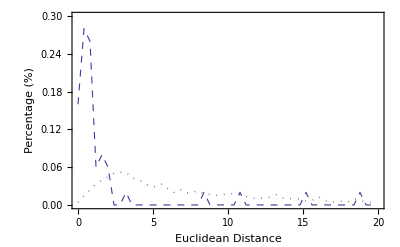

```mathematica
(*first, use one group of data as templ*)
pdata=pm[[All,1]];
templ=pm[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
(*For[i=1,i<3,i=i+0.002,
{far,frr}=VF[tg,classifyDist1[pdata,templ,i]][[{2,3}]];
If[Abs[far-frr]≤0.004,Break[]];
];*)
EER[templ,pdata,tg,classifyDist1,{1,3,0.002}]
```

{2.032,{0.120408,0.12}}

```mathematica
(*VF[tg,classifyDist1[pdata,templ,0]]*)
```

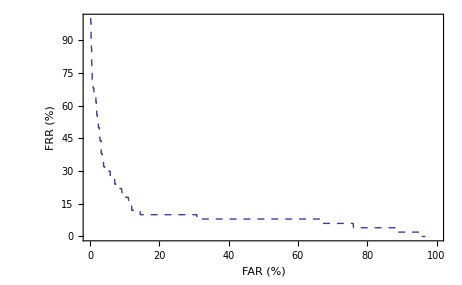

```mathematica
r1=RocPlot[pdata,templ,tg,classifyDist1,{0,20,0.2},0];
```

```mathematica
(* try second method :食指-无名指*)
pm2=pd[[All,All,2]];
Dimensions[%]
```

{50,2,46}

```mathematica
{ddiff,dsame}=eucDist[pm2];
{ns,nd}={Length[dsame],Length[ddiff]}

Min[dsame]
Max[dsame]
mdsame=Mean[dsame]
ddsame=StandardDeviation[dsame]

Min[ddiff]
Max[ddiff]
mddiff=Mean[ddiff]
dddiff=StandardDeviation[ddiff]
```

{50,4900}

0.132138

11.065

1.43602

2.08609

0.223193

32.134

7.83777

5.60804

```mathematica
dx=0.3;
dds=BinCounts[dsame,{0,20,dx}]/ns;
ddd=BinCounts[ddiff,{0,20,dx}]/nd;

dist=Table[i*dx,{i,0,Length[ddd]-1}];
pdds=Transpose[{dist,dds}];
pddd=Transpose[{dist,ddd}];
```

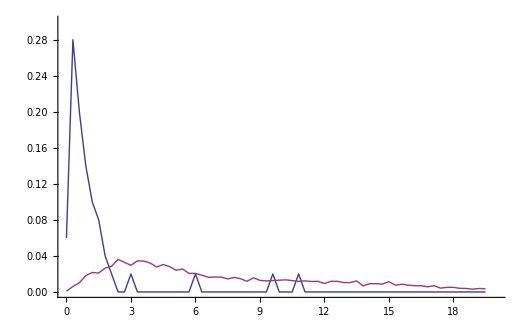

```mathematica
p50=ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.3}}]
```

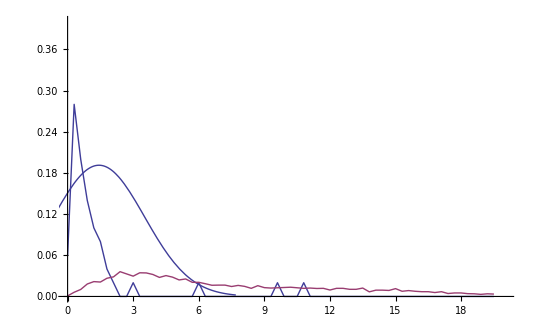

```mathematica
Ppdf1=Plot[PDF[NormalDistribution[mdsame,ddsame],x],{x,mdsame-3ddsame,mdsame+3ddsame}];

(*Ppdf2=Plot[1*PDF[NormalDistribution[mddiff,dddiff],x],{x,mddiff-3dddiff,mddiff+3dddiff}];*)

Show[Ppdf1, (*Ppdf2,*)p50,PlotRange->{{0,20},{0,0.4}}]
```

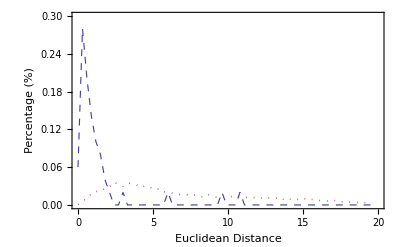

```mathematica
ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.3}},Frame->True,FrameLabel->{"Euclidean Distance","Percentage (%)"},PlotStyle->{{Dashed,Thickness[0.002]},{Dotted,Thickness[0.003]}},PlotLegend->{"Innerclass", "Interclass"},LegendShadow->None,LegendSize->{0.45,0.2},LegendPosition->{0.35,0.35}]
```

```mathematica
(*first, use one group of data as templ*)
pdata=pm2[[All,1]];
templ=pm2[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
EER[pdata,templ,tg,classifyDist1,{1,3,0.002}]
```

{2.044,0.0971429,0.1}

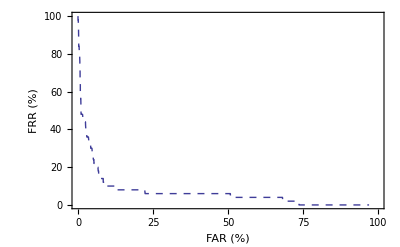

```mathematica
r2=RocPlot[pdata,templ,tg,classifyDist1,{0,20,0.1},0];
```

```mathematica
(* try third method :食指-小指*)
```

```mathematica
pm3=pd[[All,All,3]];
Dimensions[%]
```

{50,2,46}

```mathematica
{ddiff,dsame}=eucDist[pm3];
{ns,nd}={Length[dsame],Length[ddiff]}

Min[dsame]
Max[dsame]
mdsame=Mean[dsame]
ddsame=StandardDeviation[dsame]
Min[ddiff]
Max[ddiff]
mddiff=Mean[ddiff]
dddiff=StandardDeviation[ddiff]
```

{50,4900}

0.153367

10.8205

1.72163

2.49755

0.199345

32.0282

7.8008

5.65687

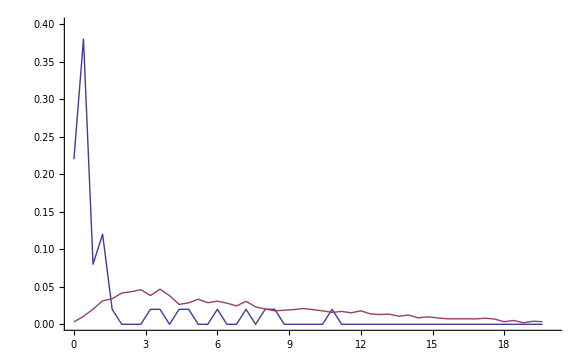

```mathematica
dx=0.4;
dds=BinCounts[dsame,{0,20,dx}]/ns;
ddd=BinCounts[ddiff,{0,20,dx}]/nd;

dist=Table[i*dx,{i,0,Length[ddd]-1}];
pdds=Transpose[{dist,dds}];
pddd=Transpose[{dist,ddd}];
p50=ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.4}}]
```

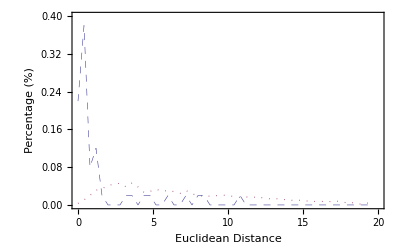

```mathematica
ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.4}},Frame->True,FrameLabel->{"Euclidean Distance","Percentage (%)"},PlotStyle->{{Dashed,Thickness[0.001]},{Dotted,Thickness[0.002]}},PlotLegend->{"Innerclass", "Interclass"},LegendShadow->None,LegendSize->{0.45,0.2},LegendPosition->{0.3,0.35}]
```

```mathematica
pdata=pm3[[All,1]];
templ=pm3[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
EER[pdata,templ,tg,classifyDist1,{1,3,0.002}]
```

{2.75,0.179592,0.18}

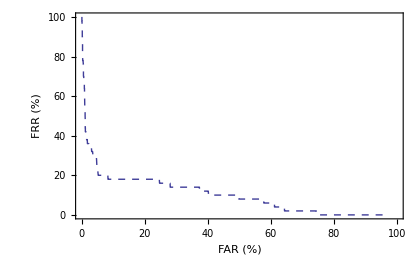

```mathematica
r3=RocPlot[pdata,templ,tg,classifyDist1,{0,20,0.1},0];
```

```mathematica
(* try forth method :中指-无名指*)
```

```mathematica
pm4=pd[[All,All,4]];
Dimensions[%]
```

{50,2,46}

```mathematica
{ddiff,dsame}=eucDist[pm4];
{ns,nd}={Length[dsame],Length[ddiff]}

Min[dsame]
Max[dsame]
mdsame=Mean[dsame]
ddsame=StandardDeviation[dsame]
Min[ddiff]
Max[ddiff]
mddiff=Mean[ddiff]
dddiff=StandardDeviation[ddiff]
```

{50,4900}

0.243752

8.84762

1.28499

1.8304

0.262217

29.5602

7.91702

5.49685

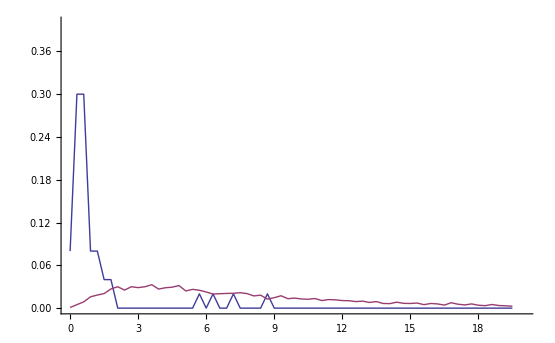

```mathematica
dx=0.3;
dds=BinCounts[dsame,{0,20,dx}]/ns;
ddd=BinCounts[ddiff,{0,20,dx}]/nd;

dist=Table[i*dx,{i,0,Length[ddd]-1}];
pdds=Transpose[{dist,dds}];
pddd=Transpose[{dist,ddd}];
p50=ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.4}}]
```

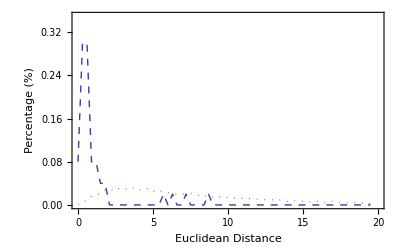

```mathematica
ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.35}},Frame->True,FrameLabel->{"Euclidean Distance","Percentage (%)"},PlotStyle->{{Dashed(*,Thickness[0.001]*)},{Dotted(*,Thickness[0.002]*)}},PlotLegend->{"Innerclass", "Interclass"},LegendShadow->None,LegendSize->{0.45,0.2},LegendPosition->{0.35,0.35}]
```

```mathematica
pdata=pm4[[All,1]];
templ=pm4[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
EER[pdata,templ,tg,classifyDist1,{1.6,2.5,0.0005}]
```

{1.994,0.084898,0.08}

```mathematica
VF[tg,classifyDist1[pdata,templ,1.995]]
```

{0.0848,0.084898,0.08}

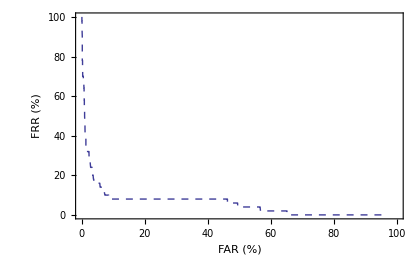

```mathematica
r4=RocPlot[pdata,templ,tg,classifyDist1,{0,20,0.1},0];
```

```mathematica
(* try fifth method: 中指-小指*)
```

```mathematica
pm5=pd[[All,All,5]];
Dimensions[%]
```

{50,2,46}

```mathematica
{ddiff,dsame}=eucDist[pm5];
{ns,nd}={Length[dsame],Length[ddiff]}

Min[dsame]
Max[dsame]
mdsame=Mean[dsame]
ddsame=StandardDeviation[dsame]
Min[ddiff]
Max[ddiff]
mddiff=Mean[ddiff]
dddiff=StandardDeviation[ddiff]
```

{50,4900}

0.247304

15.1739

1.29611

2.42125

0.270639

35.0821

7.76192

5.71158

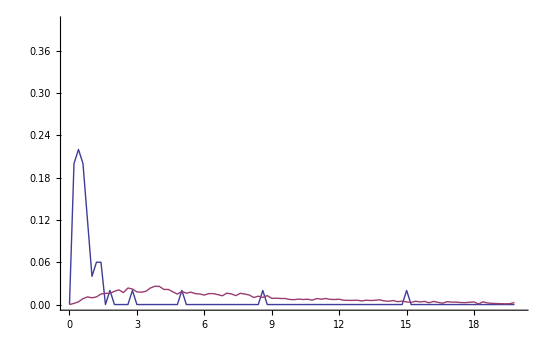

```mathematica
dx=0.2;
dds=BinCounts[dsame,{0,20,dx}]/ns;
ddd=BinCounts[ddiff,{0,20,dx}]/nd;

dist=Table[i*dx,{i,0,Length[ddd]-1}];
pdds=Transpose[{dist,dds}];
pddd=Transpose[{dist,ddd}];
p50=ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.4}}]
```

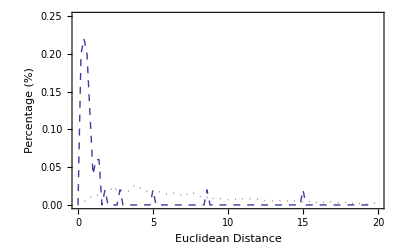

```mathematica
ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.25}},Frame->True,FrameLabel->{"Euclidean Distance","Percentage (%)"},PlotStyle->{{Dashed(*,Thickness[0.001]*)},{Dotted(*,Thickness[0.002]*)}},PlotLegend->{"Innerclass", "Interclass"},LegendShadow->None,LegendSize->{0.45,0.2},LegendPosition->{0.35,0.35}]
```

```mathematica
pdata=pm5[[All,1]];
templ=pm5[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
EER[pdata,templ,tg,classifyDist1,{1,2,0.0005}]
```

{1.8185,0.0771429,0.08}

```mathematica
VF[tg,classifyDist1[pdata,templ,1.84]]
```

{0.08,0.08,0.08}

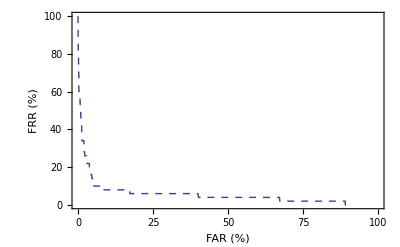

```mathematica
r5=RocPlot[pdata,templ,tg,classifyDist1,{0,20,0.1},0];
```

```mathematica
(* try sixth method: 无名指-小指*)
```

```mathematica
pm6=pd[[All,All,6]];
Dimensions[%]
```

{50,2,46}

```mathematica
{ddiff,dsame}=eucDist[pm6];
{ns,nd}={Length[dsame],Length[ddiff]}

Min[dsame]
Max[dsame]
mdsame=Mean[dsame]
ddsame=StandardDeviation[dsame]
Min[ddiff]
Max[ddiff]
mddiff=Mean[ddiff]
dddiff=StandardDeviation[ddiff]
```

{50,4900}

0.232137

13.276

1.65407

2.4071

0.27164

29.1656

7.91132

5.50183

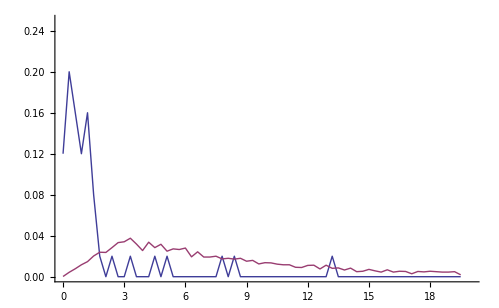

```mathematica
dx=0.3;
dds=BinCounts[dsame,{0,20,dx}]/ns;
ddd=BinCounts[ddiff,{0,20,dx}]/nd;
dist=Table[i*dx,{i,0,Length[ddd]-1}];
pdds=Transpose[{dist,dds}];
pddd=Transpose[{dist,ddd}];
p50=ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.25}}]
```

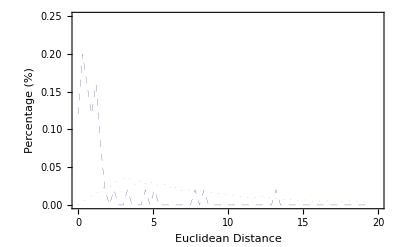

```mathematica
ListPlot[{pdds,pddd},Joined->True,PlotRange->{{0,20},{0,0.25}},Frame->True,FrameLabel->{"Euclidean Distance","Percentage (%)"},PlotStyle->{{Dashed,Thickness[0.0005]},{Dotted,Thickness[0.0005]}},PlotLegend->{"Innerclass", "Interclass"},LegendShadow->None,LegendSize->{0.45,0.2},LegendPosition->{0.35,0.35}]
```

```mathematica
pdata=pm6[[All,1]];
templ=pm6[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
EER[pdata,templ,tg,classifyDist1,{1,3,0.001}]
```

{2.512,0.115102,0.12}

```mathematica
VF[tg,classifyDist1[pdata,templ,2.558]]
```

{0.12,0.12,0.12}

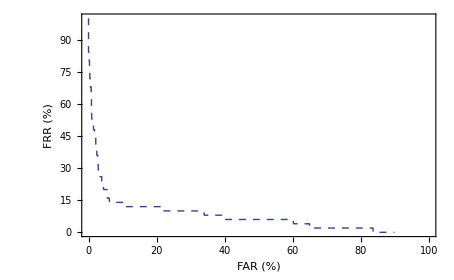

```mathematica
r6=RocPlot[pdata,templ,tg,classifyDist1,{0,20,0.1},0];
```

```mathematica
(*Tooltip[r1,"1"]*)
```

```mathematica
(*gg=GraphicsGrid[{{r1,r2,r3},{r4,r5,r6}}];*)
```

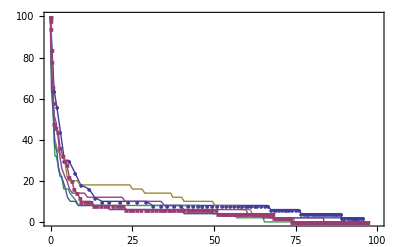

```mathematica
ListPlot[{r1,r2,r3,r4,r5,r6},Joined->True,PlotRange->{{0,100},{0,100}},PlotMarkers->{Automatic,5},Frame->True,FrameLabel->{"FAR (%)","FRR (%)"},
PlotLegend->{"m1","m2","m3","m4","m5","m6"},LegendShadow->None,LegendSize->{0.2,0.45},LegendPosition->{0.55,0.05}]
```

```mathematica
r1
r2
r3
r4
r5
r6
```

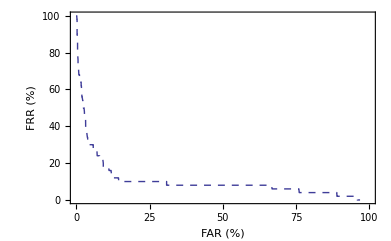
```mathematica
r1=-Graphics-;
```

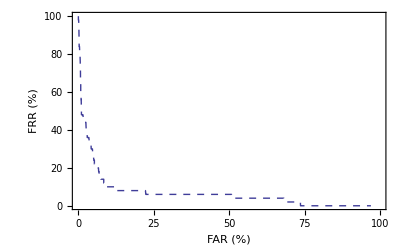
```mathematica
r2=-Graphics-;
```

```mathematica
(*Show[r1,r2,r3,r4,r5,r6,PlotRange->{{0,50},{0,50}},AspectRatio->0.8]*)
Show[r1,r2]
(*Show[r4,r5,r6];*)
```